# Bootstrap Stats

```mathematica
Clear["Global`*"]
```

### Set Up BCa

BCa method from An Introduction to the Bootstrap by B. Efron and R. J. Tibshirani Chapter 11 and 14

```mathematica
booterdata=ToExpression[Import[NotebookDirectory[]<>"booterdata.csv"]]; (*import booterstrap data from bootstrap run*)
bestfit={aX->0.07243165880437435,wX->0.0026142991079086157,pX->27.700459925037663,ynX->0.060192963245436854,dsX->0.7709975010970849,dhX->0.12619563820188512,h0X->6.502940605096842*^-6,s0X->1.0227841615913929*^-10,rcX->0.009992087726261166,rnX->0.014645292219590888}; (*best fit parameters for full data*) 
z0[dat_,θ_]:= 
N[InverseCDF[NormalDistribution[0,1],Count[dat,u_/;u<θ]/Length[dat]]](*Equation 14.14 *)
α[dat_]:=(*Equation 14.15*)
Module[{l,θi,θdot,top},
l=Length[dat];
θi=Table[Mean[Delete[dat,{i}]],{i,1,l}];(*Equation 11.2*)
θdot=Total[θi]/l;(*Equation 11.4*)
top=Sum[(θdot-θi[[i]])^3,{i,1,l}];(*numerator of Equation 14.15*)
N[top/(6 (Sum[(θdot-θi[[i]])^2,{i,1,l}])^(3/2))]] (*Full Equation 14.15*)
α1[z0_,a_]:=CDF[NormalDistribution[0,1],z0+(z0+InverseCDF[NormalDistribution[],0.05])/(1-a (InverseCDF[NormalDistribution[],0.05]))] (*top Equation 14.10*)
α2[z0_,a_]:=CDF[NormalDistribution[0,1],z0+(z0+InverseCDF[NormalDistribution[],0.95])/(1-a (InverseCDF[NormalDistribution[],0.95]))](*bottom Equation 14.10*)
pull[var_,booterlist_]:=Module[{pos},
pos=Position[booterlist[[1,2]],var][[1,1]];
Table[booterlist[[i,2,pos,2]],{i,1,Length[booterlist]}]]
(* function pull data from bootstrapping data*)
ci[par_,dat_]:=(*calculate Confidence Intervals*)
Module[{list,θ,z0X,αX,α1X,α2X,minval,maxval},
θ=bestfit[[Position[bestfit,par][[1,1]],2]];(*best fit values*)
list=Sort[pull[par,dat]]; (*extract data from bootstrap run*)
z0X=z0[list,θ];(*calculate the z0 value*)
αX=α[list];(*calculate α*)
α1X=α1[z0X,αX]; (*calculate α1*)
α2X=α2[z0X,αX];(*calculate α2*)
minval=If[Round[ α1X Length[list]]==0,1,Round[ α1X Length[list]]];(*Find position of lower bound*)
maxval=Round[ α2X Length[list]];(*Find position of upper bound*)
{par,θ,{Take[list,{minval}][[1]],Take[list,{maxval}][[1]]}}](*output list with parameter name, best fitted value and confidence interval bounds*)
```

### Calculate Confidence Intervals

```mathematica
cidat=ci[#,booterdata]&/@bestfit[[All,1]] (*complete CI for all parameters*)
```

{{aX,0.0724317,{0.0408535,0.107856}},{wX,0.0026143,{0.00165017,0.0044584}},{pX,27.7005,{11.7174,50.1507}},{ynX,0.060193,{0.0294746,0.101222}},{dsX,0.770998,{0.514272,1.24908}},{dhX,0.126196,{0.104612,0.156239}},{h0X,6.50294×10^-6,{5.86183×10^-6,7.41485×10^-6}},{s0X,1.02278×10^-10,{1.00017×10^-10,1.03394×10^-10}},{rcX,0.00999209,{0.00903834,0.0109297}},{rnX,0.0146453,{0.00265087,0.0292784}}}

### Histograms

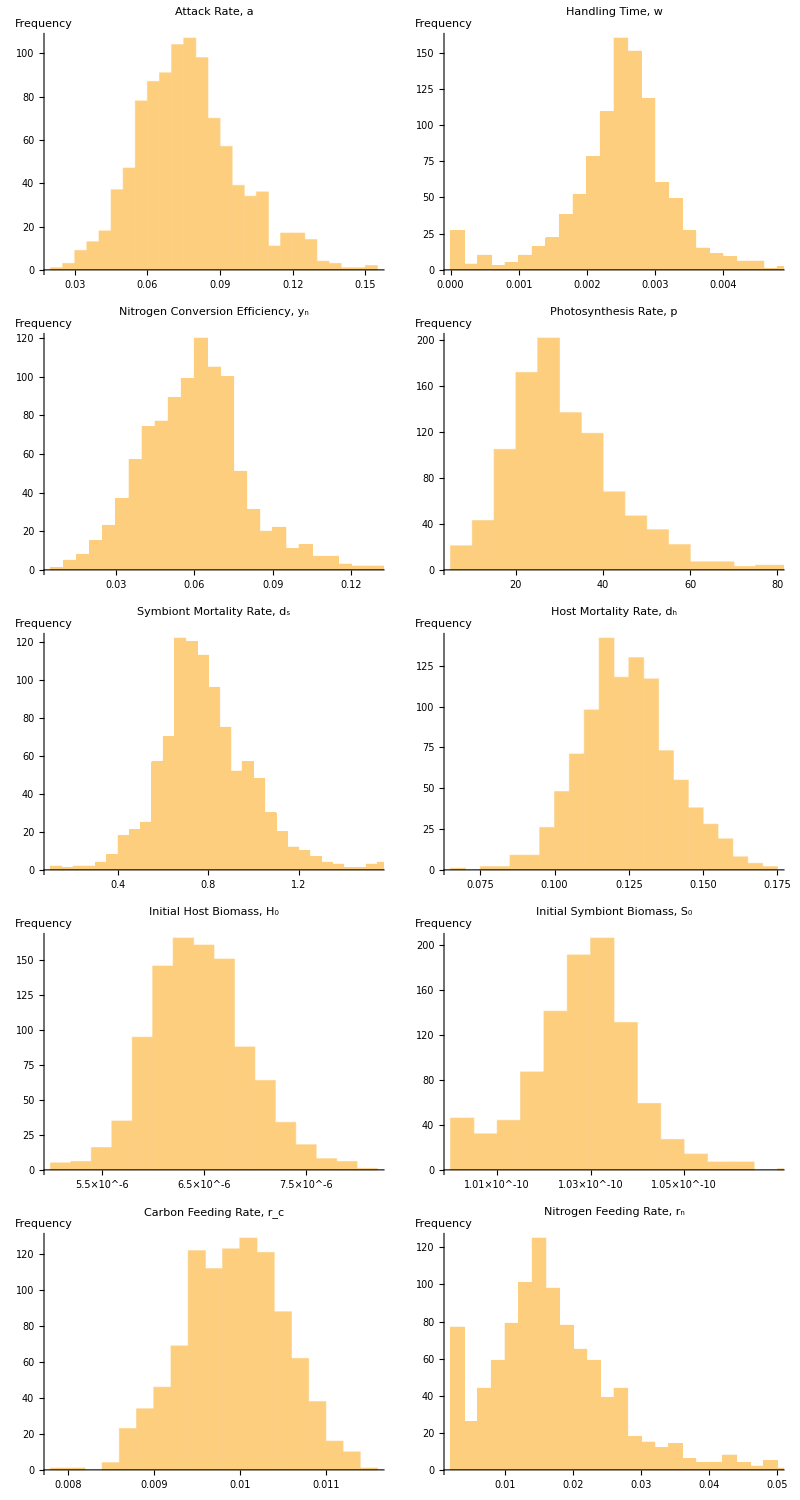

```mathematica
hist[data_,label_,xlabel_]:=
Histogram[data,PlotLabel->Style[label,FontSize->15],AxesLabel->{Null,"Frequency"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->10},ImageSize->250] (*set up universal histogram function*)
ahist=hist[pull[aX,booterdata],"Attack Rate, a","a"]; (*attack rate*)
whist=hist[pull[wX,booterdata],"Handling Time, w","w"];(*handeling time*)
phist=hist[pull[pX,booterdata],"Photosynthesis Rate, p","p"]; (*photosynthesis rate*)
ynhist=hist[pull[ynX,booterdata],"Nitrogen Conversion Efficiency," Subscript["y","n"],Subscript["y","n"]]; (*nitrogen conversion efficiency*)
dshist=hist[pull[dsX,booterdata],Join["Symbiont Mortality Rate, "Subscript["d","s"]],Subscript["d","s"]];(*symbiont mortality*)
dhhist=hist[pull[dhX,booterdata],Join["Host Mortality Rate, "Subscript["d","h"]],Subscript["d","h"]];(*host mortality*)
h0hist=Quiet[Histogram[pull[h0X,booterdata],PlotLabel->Style[Join["Initial Host Biomass, "Subscript["H","0"]],FontSize->15],AxesLabel->{Null,"Frequency"},Ticks->{{0,N[5.5*10^-6],N[6.5*10^-6],N[7.5*10^-6]},Automatic},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->12},ImageSize->250]]; (*initial host biomass*)
s0hist=Histogram[pull[s0X,booterdata],PlotLabel->Style[Join["Initial Symbiont Biomass, "Subscript["S","0"]],FontSize->15],AxesLabel->{Null,"Frequency"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->12},Ticks->{{0,N[1.01*10^-10],N[1.03*10^-10],N[1.05*10^-10],N[1.08*10^-10]},Automatic},ImageSize->250](*initial host biomass*);
rchist=Histogram[pull[rcX,booterdata],PlotLabel->Style[Join["Carbon Feeding Rate, "Subscript["r","c"]],FontSize->15],AxesLabel->{Null,"Frequency"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->12},Ticks->{{0,N[0.008],N[0.009],N[0.01],N[0.011]},Automatic},ImageSize->250] (*host carbon uptake rate*);
rnhist=Histogram[pull[rnX,booterdata],PlotLabel->Style[Join["Nitrogen Feeding Rate, "Subscript["r","n"]],FontSize->15],AxesLabel->{Null,"Frequency"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},ImageSize->250](* host nitrogen uptake rate*);
booterfig=Grid[{{ahist,whist},{ynhist,phist},{dshist,dhhist},
{h0hist,s0hist},
{rchist,rnhist}}] (*Figure C.6*)
```

```mathematica
Export[NotebookDirectory[]<>"booterfig.jpg",booterfig]
```

/Users/JakobK-R/Desktop/Coral/Paper_5/booterfig.jpg

### Uncut Figure

Bootstrapping without extreme outliers removed.

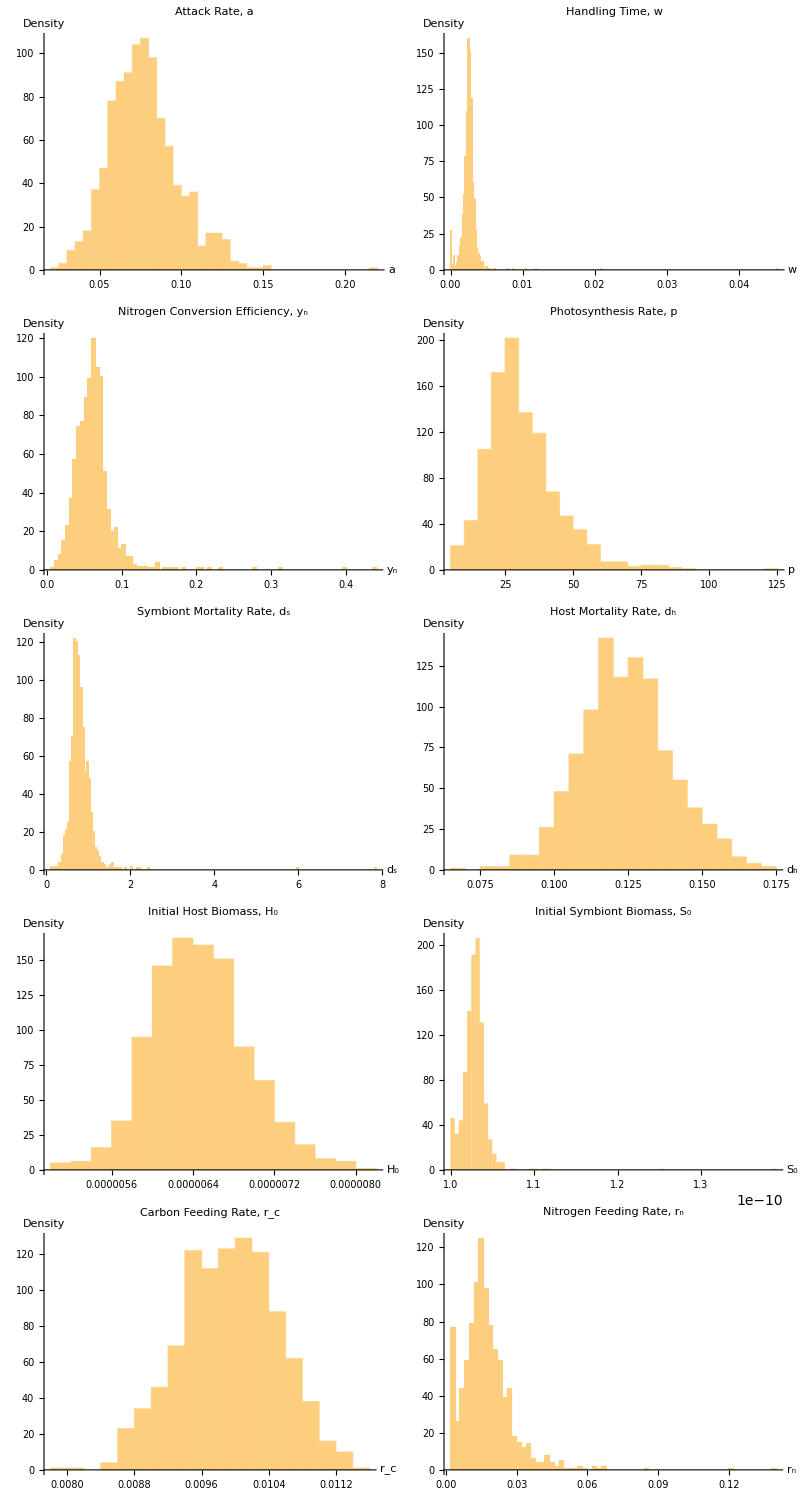

```mathematica
hist[data_,label_,xlabel_]:=
Histogram[data,PlotLabel->Style[label,FontSize->15],AxesLabel->{xlabel,"Density"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->10},PlotRange->All,ImageSize->250]
ahist=hist[pull[aX,booterdata],"Attack Rate, a","a"];
whist=hist[pull[wX,booterdata],"Handling Time, w","w"];
phist=hist[pull[pX,booterdata],"Photosynthesis Rate, p","p"];
ynhist=hist[pull[ynX,booterdata],"Nitrogen Conversion Efficiency," Subscript["y","n"],Subscript["y","n"]];
dshist=hist[pull[dsX,booterdata],Join["Symbiont Mortality Rate, "Subscript["d","s"]],Subscript["d","s"]];
dhhist=hist[pull[dhX,booterdata],Join["Host Mortality Rate, "Subscript["d","h"]],Subscript["d","h"]];
h0hist=Quiet[Histogram[pull[h0X,booterdata],PlotLabel->Style[Join["Initial Host Biomass, "Subscript["H","0"]],FontSize->15],AxesLabel->{Subscript["H","0"],"Density"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->12},ImageSize->250,PlotRange->All]];
s0hist=Histogram[pull[s0X,booterdata],PlotLabel->Style[Join["Initial Symbiont Biomass, "Subscript["S","0"]],FontSize->15],AxesLabel->{Subscript["S","0"],"Density"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->12}(*Ticks->{{0,N[2*10^-10],N[3.5*10^-10],N[5*10^-10],N[6.5*10^-10]},Range[0,120,20]}*),ImageSize->250,PlotRange->All];
rchist=hist[pull[rcX,booterdata],Join["Carbon Feeding Rate, "Subscript["r","c"]],Subscript["r","c"]];
rnhist=Histogram[pull[rnX,booterdata],PlotLabel->Style[Join["Nitrogen Feeding Rate, "Subscript["r","n"]],FontSize->15],AxesLabel->{Subscript["r","n"],"Density"},LabelStyle->{FontFamily->"Times New Roman",FontColor->Black,FontSize->15},ImageSize->250,PlotRange->All];
booterfig=Grid[{{ahist,whist},
{ynhist,phist},{dshist,dhhist},
{h0hist,s0hist},
{rchist,rnhist}}]
```